```mathematica
Clear["Global`*"];
```

```mathematica
data=Import["../res/data_000000_000000.dat"];
tdc=data⟦1⟧//First;
data=data⟦2;;⟧;
time=data⟦;;,1⟧;
Print["data number: ",Length@time]
```

data number: 2369

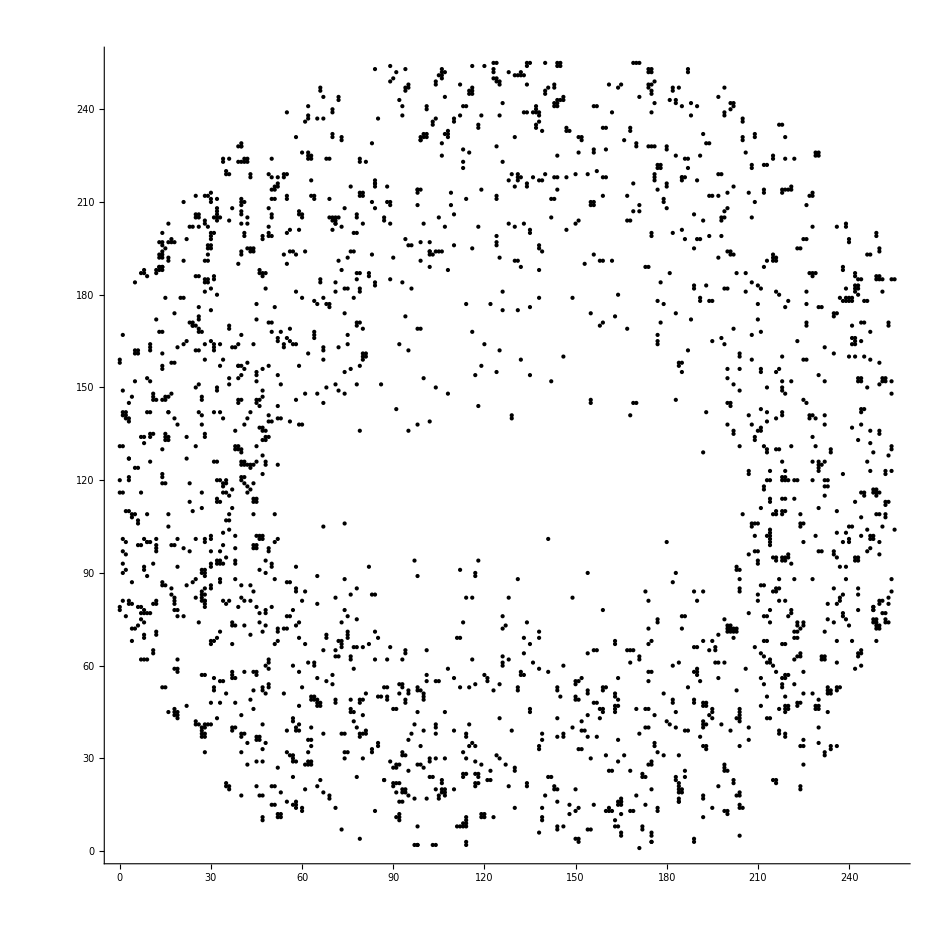

```mathematica
(* 2D scattering *)
r=Thread[{data⟦;;,3⟧,data⟦;;,4⟧}];
Graphics[Point[r,VertexColors->(Hue/@Rescale[time])],Axes->True,GridLines->{Range[250],Range[250]}]
```

```mathematica
(* 3D scattering *)
r=Thread[{data⟦;;,1⟧,data⟦;;,3⟧,data⟦;;,4⟧}];
Graphics3D[Point[r,VertexColors->(Hue/@Rescale[time])],Axes->True,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
data1=Import["/home/tianmin/Desktop/group/Tpx3Cam/simple_cluster_analysis/tpx-data-proc/test.dat"];
r1=data1⟦;;,{3,4}⟧;
```

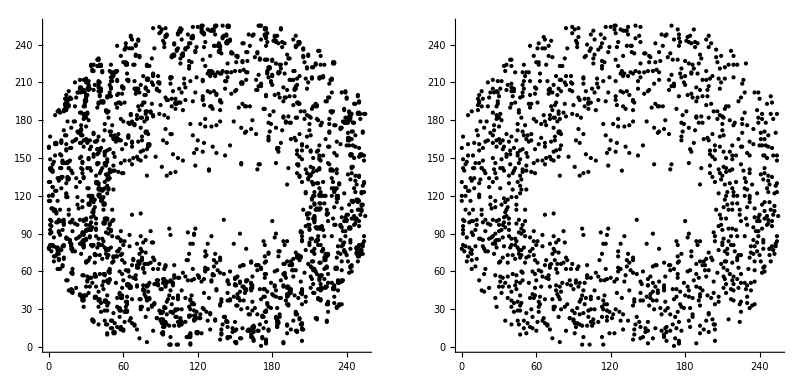

```mathematica
r=Thread[{data⟦;;,3⟧,data⟦;;,4⟧}];
GraphicsRow[{
Graphics[Point[r,VertexColors->(Hue/@Rescale[time])],Axes->True,GridLines->{Range[250],Range[250]}],
Graphics[Point[r1,VertexColors->(Hue/@Rescale[data1⟦;;,1⟧])],Axes->True,GridLines->{Range[250],Range[250]}]}]
```

```mathematica
test = {{1,2,3,4},{5,6,7,8}};
test⟦;;,{1,3,4}⟧
```

{{1,3,4},{5,7,8}}